```mathematica
$VersionNumber
$System
```

8.

Linux x86 (64-bit)

```mathematica
$LoadFeynArts=True;
<<FeynCalc`;
$FAVerbose=0;
FAPatch[PatchModelsOnly->True]
```

FeynCalc 9.0.1. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, TUM-EFT 71/15, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

Patching FeynArts models... done!

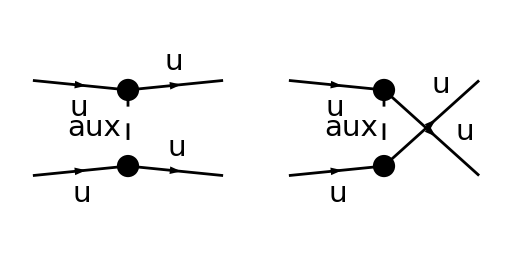

```mathematica
top=CreateTopologies[0,2->2];
diags=InsertFields[top,{F[3,{1}],F[3,{1}]}->{F[3,{1}],F[3,{1}]},InsertionLevel->{Particles},Model->"model1",GenericModel->"model1",ExcludeParticles->{V[1],V[2],V[3]}];
Paint[%, ColumnsXRows -> {2, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
AmpList=FCFAConvert[CreateFeynAmp[diags],ChangeDimension->4,IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},DropSumOver->True,List->False,UndoChiralSplittings->True,FinalSubstitutions->Flatten[Join[M$FACouplings,{SUNFDelta[__]:>1}]],SMP->True]//Contract
```

((φ(OverBar[k1],m_u)).(γ̄)^Lor1.(γ̄)^7.(φ(OverBar[p2],m_u)) (φ(OverBar[k2],m_u)).(γ̄)^Lor1.(γ̄)^7.(φ(OverBar[p1],m_u)))/((OverBar[k1]-OverBar[p2])^2-MAUX^2)-((φ(OverBar[k1],m_u)).(γ̄)^Lor2.(γ̄)^7.(φ(OverBar[p1],m_u)) (φ(OverBar[k2],m_u)).(γ̄)^Lor2.(γ̄)^7.(φ(OverBar[p2],m_u)))/((OverBar[k2]-OverBar[p2])^2-MAUX^2)